Caso “ibrido” di un sistema dinamico che presenta autovalori reali e compliessi e coniugati (TC)

```mathematica
A={{-9/2,3,1/2},{-1,-1,0},{-5/2,5,-3/2}}
```

{{-9/2,3,1/2},{-1,-1,0},{-5/2,5,-3/2}}

```mathematica
C1={1,0,0}
```

{1,0,0}

Calcolo gli autovalori di A

```mathematica
λ=Eigenvalues[A]
```

{-3,-2+ⅈ,-2-ⅈ}

```mathematica
CharacteristicPolynomial[A,x]
```

-15-17 x-7 x^2-x^3

```mathematica
Simplify[A.A.A+7A.A+17 A+15 IdentityMatrix[3]]
```

{{0,0,0},{0,0,0},{0,0,0}}

Costruisco la matrice di cambiamento di base, inizio dalla funzione Eigenvectors di Mathematica

```mathematica
T0=Transpose[Eigenvectors[A]]
```

{{2,2/5+ⅈ/5,2/5-ⅈ/5},{1,1/10+(3 ⅈ)/10,1/10-(3 ⅈ)/10},{0,1,1}}

```mathematica
T0//MatrixForm
```

(2 | 2/5+ⅈ/5 | 2/5-ⅈ/5
1 | 1/10+(3 ⅈ)/10 | 1/10-(3 ⅈ)/10
0 | 1 | 1)

```mathematica
T=Transpose[{T0[[All,1]],Re[T0[[All,2]]],Im[T0[[All,2]]]}]
```

{{2,2/5,1/5},{1,1/10,3/10},{0,1,0}}

```mathematica
T//MatrixForm
```

(2 | 2/5 | 1/5
1 | 1/10 | 3/10
0 | 1 | 0)

Verifichiamo che la forma canonica e’ diagonale a blocchi

```mathematica
Λ=Simplify[Inverse[T].A.T]
```

{{-3,0,0},{0,-2,1},{0,-1,-2}}

```mathematica
Λ//MatrixForm
```

(-3 | 0 | 0
0 | -2 | 1
0 | -1 | -2)

Calcolo la risposta libera nello stato a partire dallo stato iniziale

```mathematica
Subscript[x, 0]={{1},{0},{0}}
```

{{1},{0},{0}}

Proietto lo stato iniziale lungo le colonne della matrice “ibrida” T

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{3/4},{0},{-5/2}}

```mathematica
σ=Re[λ[[2]]]
```

-2

```mathematica
ω=Im[λ[[2]]]
```

1

Calcolo la risposta libera sfruttando la decomposizione modale

```mathematica
Subscript[x, l][t_]:=Simplify[T.({{Exp[λ[[1]]t], 0, 0}, {0, Exp[σ t]Cos[ω t], Exp[σ t]Sin[ω t]}, {0, Exp[σ t]Sin[ω t], Exp[σ t]Cos[ω t]}}).Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]//MatrixForm
```

(-1/2 ⅇ^(-3 t) (-3+ⅇ^t Cos[t]+2 ⅇ^t Sin[t])
-1/4 ⅇ^(-3 t) (-3+3 ⅇ^t Cos[t]+ⅇ^t Sin[t])
-5/2 ⅇ^(-2 t) Sin[t])

```mathematica
Subscript[y, l][t_]:=C1.Subscript[x, l][t]
```

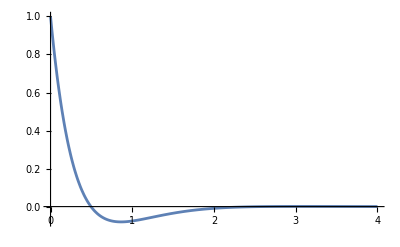

```mathematica
Plot[Subscript[y, l][t],{t,0,4},PlotRange->All]
```

```mathematica
T//MatrixForm
```

(2 | 2/5 | 1/5
1 | 1/10 | 3/10
0 | 1 | 0)

Analizziamo cosa accade quando “cambia” lo stato iniziale

```mathematica
Subscript[x, 0]={{-4},{-2},{0}}
```

{{-4},{-2},{0}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{-2},{0},{0}}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{{-4 ⅇ^(-3 t)},{-2 ⅇ^(-3 t)},{0}}

```mathematica
T//MatrixForm
```

(2 | 2/5 | 1/5
1 | 1/10 | 3/10
0 | 1 | 0)

```mathematica
Subscript[x, 0]={{1/5},{-1/5},{1}}
```

{{1/5},{-1/5},{1}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{0},{1},{-1}}

```mathematica
Subscript[x, l][t_]:=Simplify[T.MatrixExp[Λ t].Subscript[z, 0]]
```

```mathematica
Subscript[x, l][t]
```

{{1/5 ⅇ^(-2 t) (Cos[t]-3 Sin[t])},{-1/5 ⅇ^(-2 t) (Cos[t]+2 Sin[t])},{ⅇ^(-2 t) (Cos[t]-Sin[t])}}

```mathematica
g2=Graphics3D[InfinitePlane[{0,0,0},{T[[All,2]],T[[All,3]]}]];
```

```mathematica
g1=ParametricPlot3D[Subscript[x, l][t],{t,0,5},PlotRange->All,PlotStyle->Red];
```

```mathematica
Show[g1,g2]
```

-Graphics3D-